## 操作列表

在 Wolfram 语言中，有数以千计的函数可以用来处理列表。

你可以用列表来进行算术运算：

```mathematica
{1,2,3}+10
```

{11,12,13}

```mathematica
{1,1,2}*{1,2,3}
```

{1,2,6}

计算前10个数的平方：

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

绘制前20个数的平方：

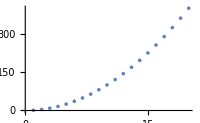

```mathematica
ListPlot[Range[20]^2]
```

Sort 用于将一个列表按顺序排列：

```mathematica
Sort[{4,2,1,3,6}]
```

{1,2,3,4,6}

Length 用于计算列表的长度：

```mathematica
Length[{5,3,4,5,3,4,5}]
```

7

Total 用于计算列表的总和：

```mathematica
Total[{1,1,2,2}]
```

6

计算从1到10的数字的总和：

```mathematica
Total[Range[10]]
```

55

Count 用于计算某个对象在列表中出现的次数。

计算 a 在列表中出现的次数：

```mathematica
Count[{a,b,a,a,c,b,a},a]
```

4

得到一个列表中的某个元素往往很有用。First 将给出第一个元素；Last 将给出最后一个元素。Part 将给出某个特定位置上的元素。

取出列表中的第一个元素：

```mathematica
First[{7,6,5}]
```

7

取出列表中的最后一个元素：

```mathematica
Last[{7,6,5}]
```

5

取出第 2 个元素：

```mathematica
Part[{7,6,5},2]
```

6

从你排序后的列表中取出第一个元素，与寻找最小元素是一样的：

```mathematica
First[Sort[{6,7,1,2,4,5}]]
```

1

```mathematica
Min[{6,7,1,2,4,5}]
```

1

如果你有一个数字，比如 5671，你可以用 IntegerDigits[5671] 来创建它每位数字的列表。

将一个数字分解成数字列表：

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

找到最后一位数字：

```mathematica
Last[IntegerDigits[1988]]
```

8

Take 让你从一个列表的起始位置开始取出指定数量的元素：

从一个列表中取前3个元素：

```mathematica
Take[{101,203,401,602,332,412},3]
```

{101,203,401}

取出 2 的 100 次幂的前 10 位数字：

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

Drop 将去掉列表开始位置的元素。

```mathematica
Drop[{101,203,401,602,332,412},3]
```

{602,332,412}

词汇

{2,3,4}+{5,6,2} |   | 对列表进行数学计算
Sort[{5,7,1}] |   | 对列表进行排序
Length[{3,3}] |   | 列表长度(元素个数)
Total[{1,1,2}] |   | 列表中的所有元素总和
Count[{3,2,3},3] |   | 计算一个元素的出现次数
First[{2,3}] |   | 列表中的第一个元素
Last[{6,7,8}] |   | 列表中的最后一个元素
Part[{3,1,4},2] |   | 列表的特定部分，也可以写作 {3,1,4}[[2]]
Take[{6,4,3,1},2] |   | 从列表的开头提取元素
Drop[{6,4,3,1},2] |   | 从列表的开头删除元素
IntegerDigits[1234] |   | 数字的各位数字列表

"共有 14 道习题"
"以及 7 道附加题" | "开始练习 »"

按相反的顺序列出前 10 个数字的平方。»

| 期望输出： |  
  | {100,81,64,49,36,25,16,9,4,1} |

求前 10 的数字的平方和。»

| 期望输出： |  
  | 385 |

从 1 开始，绘制前 10 个数字的平方的点集图。»

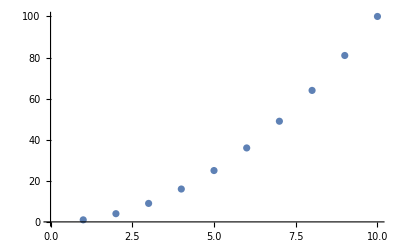
| 期望输出： |  
  | -Graphics- |

使用 Sort、Join 和 Range 来创建 {1,1,2,2,3,3,4,4}。»

| 期望输出： |  
  | {1,1,2,2,3,3,4,4} |

使用 Range 和 + 来创建一个从 10(含) 到 20(含) 的列表。»

| 期望输出： |  
  | {10,11,12,13,14,15,16,17,18,19,20} |

将前五个数字的平方与立方按顺序排列在一个列表中。»

| 期望输出： |  
  | {1,1,4,8,9,16,25,27,64,125} |

计算 2^128 的位数。»

| 期望输出： |  
  | 39 |

计算 2^32 的第一位数字。»

| 期望输出： |  
  | 4 |

计算 2^100 的前 10 位数字。»

| 期望输出： |  
  | {1,2,6,7,6,5,0,6,0,0} |

找出 2^20 的各位数字中出现的最大值。»

| 期望输出： |  
  | 8 |

找出 2^1000 中出现了多少个零。»

| 期望输出： |  
  | 28 |

使用 Part、Sort 和 IntegerDigits 来找出 2^20 中第二小的位数。»

| 期望输出： |  
  | 1 |

创建 2^128 中出现的各位数字的线条图。»

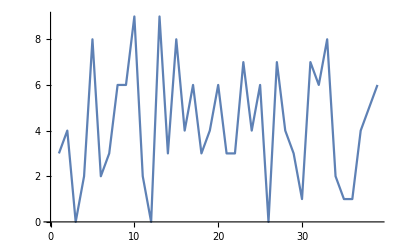
| 期望输出： |  
  | -Graphics- |

使用 Take 和 Drop 从 Range[100] 中取出 11 到 20。»

| 期望输出： |  
  | {11,12,13,14,15,16,17,18,19,20} |

创建前 10 个 3 的倍数的列表。»

| 期望输出： |  
  | {3,6,9,12,15,18,21,24,27,30} |

只用 Range 和 Times 创建出前 10 个数字的平方的列表。»

| 期望输出： |  
  | {1,4,9,16,25,36,49,64,81,100} |

计算 2^37 的最后一位。»

| 期望输出： |  
  | 2 |

找到 2^32 的倒数第二位。»

| 期望输出： |  
  | 9 |

求 3^126 的各位数字之和。»

| 期望输出： |  
  | 234 |

将 2^32 中出现的各位数字创建为饼状图。»

| 期望输出： |  
  | -Graphics- |

分别为 2^20、2^40、2^60 中的各位数字创建一个饼状图。»

| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-} |

问&答

可以将长度不同的列表进行相加吗？

不可以，{1,2}+{1,2,3} 不会正常运行。{1,2,0}+{1,2,3} 就可以运行，如果你是这个意思。

是否存在一个什么都没有的列表？

是的。{} 就是一个长度为 0 的列表，它不包含元素。它通常被称为空列表。

技术笔记

IntegerDigits[5671] 将给出以 10 为基数的各位数字。IntegerDigits[5671,2] 将给出以2为基数的各位数字。你可以使用任何你想要的基数。FromDigits[{5,6,7,1}] 将使用数字列表来重建一个数字。

Rest[list] 给出列表中第一个元素之后的所有元素。Most[list] 将给出除最后一个以外的所有元素。

探索更多

Wolfram 语言中的列表操作指南 »